## Introduction

Rederive results in x here.

## Main

### Animation

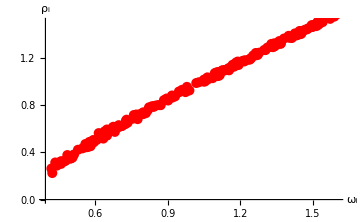
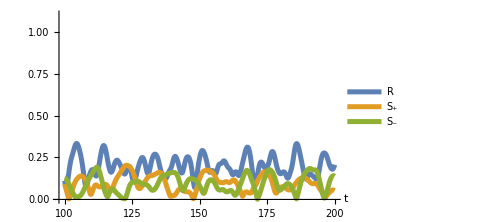
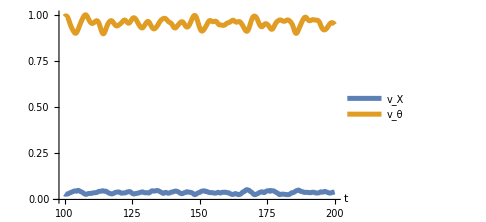
-Graphics- | -Graphics- | -Graphics-

{1.03067×10^-18,0.953151}

```mathematica
(*SeedRandom[1];*)
{dt,T,n}={0.1,200,200};
{A,B}={1,1};
{J1,k,γ}={0.5,0.2,0.6};
ω = RandomVariate[UniformDistribution[{1-γ,1+γ}],n];
z0=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
(*z0[[1,1]]=0.01;z0[[2,1]]=0.01;z0[[3,1]]=0;*)
znew=ConstantArray[0,{3,n}];

{t,NT}={0,Round[T/dt]};
results={};Dynamic[results]
{xs,ys,thetas,ts}={{},{},{},{}};
{R,Sp,Sm}={{},{},{}};
{vx,vtheta}={{},{}};
AvFreq = {};
While[t<NT,
znew=rk4[z0,rhslinearWinfreeNew,dt,J1,k,A,B,ω];
(*znew=periodizeMain[znew,1];*){x,y,θ}=znew;
{Z,Wp,Wm}=findOrderPars[znew];
z0=znew;t++;
velo=rhslinearWinfreeNew[znew,n,J1,k,A,B,ω];
PosVelo=Sqrt[velo[[1]]^2+velo[[2]]^2];
avPosVelo=Mean[PosVelo];avPhaseVelo=Mean[velo[[3]]];AppendTo[vx,avPosVelo];AppendTo[vtheta,avPhaseVelo];AppendTo[ts,t*dt];AppendTo[xs,x];AppendTo[ys,y];AppendTo[thetas,θ];AppendTo[R,Z];AppendTo[Sp,Wp];AppendTo[Sm,Wm];
If[t>Round[0.9*NT],AppendTo[AvFreq,θ/(t*dt)]];
(*results=plotResults[znew];*)
];
AvFreq=AvFreq//Mean;
results=plotResults[znew];
pp1=ListPlot[Transpose[{ω,AvFreq}],PlotStyle->{Red,PointSize[0.02]},PlotRange->{All,{0,1.5}},AxesLabel->{Style["ω_i",Bold,Italic,25],Style["ρ_i",Bold,Italic,25]},TicksStyle->Directive[Black, 20],AxesStyle->Thick,ImageSize->Medium];
cutoff=0.5*Length[ts];
pp2=ListPlot[{Transpose[{ts[[cutoff;;-1]],R[[cutoff;;-1]]//Abs}],Transpose[{ts[[cutoff;;-1]],Sp[[cutoff;;-1]]//Abs}],Transpose[{ts[[cutoff;;-1]],Sm[[cutoff;;-1]]//Abs}]},Joined->True,PlotStyle->Thickness[0.01],PlotRange->{Automatic,{0,1.1}},PlotLegends->{Style["R",25],Style["S_+",25],Style["S_-",25]},AxesLabel->{Style["t",Bold,Italic,25]},TicksStyle->Directive[Black, 20],AxesStyle->Thick,ImageSize->Medium];
pp3=ListPlot[{Transpose[{ts[[cutoff;;-1]],vx[[cutoff;;-1]]}],Transpose[{ts[[cutoff;;-1]],vtheta[[cutoff;;-1]]}]},Joined->True,PlotStyle->Thickness[0.01],PlotRange->{Automatic,Automatic},PlotLegends->{Style["v_X",25],Style["v_θ",25]},AxesLabel->{Style["t",Bold,Italic,25]},TicksStyle->Directive[Black, 20],AxesStyle->Thick,ImageSize->Medium];
pp4=Grid[{{pp1,pp2,pp3}}]
findVmean[xs,ys,thetas,dt]
```

```mathematica
AvFreq;
```

```mathematica
velo=rhslinearWinfreeNew[znew,n,J1,k,A,B,ω];
PosVelo=Sqrt[velo[[1]]^2+velo[[2]]^2];
avPosVelo=Mean[PosVelo]
avPhaseVelo=Mean[velo[[3]]]
```

0.0379963

1.35998

```mathematica
{xnew,ynew,thetanew}=znew;
xnew;
```

```mathematica
points=Transpose[{xnew,ynew}];
distancesFromOrigin=Norm/@points;
Max[distancesFromOrigin]
distanceMatrix=DistanceMatrix[points]//Flatten;
nonzerodist=Select[distanceMatrix,#!=0&];
Max[nonzerodist]
distsq=nonzerodist^2;
invdist=1/nonzerodist;
Max[invdist]
Min[invdist]
Mean[invdist]
1/Mean[invdist]
```

1.01895

1.97067

18.7126

0.507442

1.57215

0.63607

```mathematica
π/2//N
```

1.5708

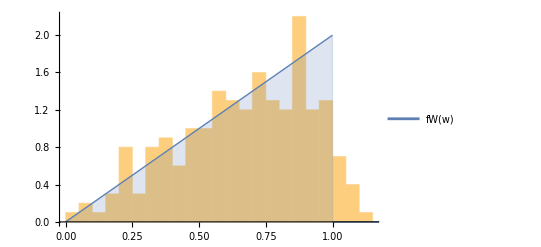

```mathematica
pk7=Histogram[distancesFromOrigin,20,"PDF"];
(*Define the PDF of W*)fW[w_]:=If[0<=w<=1,2 w,0]

(*Plot the PDF*)
pk8=Plot[fW[w],{w,0,1.2},PlotRange->All,PlotStyle->Thick,AxesLabel->{"w","f_W(w)"},PlotLabel->"PDF of W",Filling->Axis,PlotTheme->"Detailed"];

Show[pk7,pk8]
```

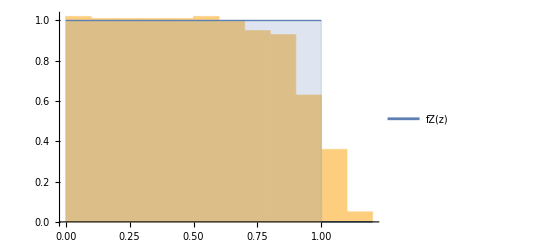

```mathematica
pk9=Histogram[distancesFromOrigin^2,10,"PDF"];
(*Define the PDF of Z*)fZ[z_]:=If[0<=z<=1,1,0]

(*Plot the PDF*)
pk10=Plot[fZ[z],{z,0,1.2},PlotRange->All,PlotStyle->Thick,AxesLabel->{"z","f_Z(z)"},PlotLabel->"PDF of Z",Filling->Axis,PlotTheme->"Detailed"];

Show[pk9,pk10]
```

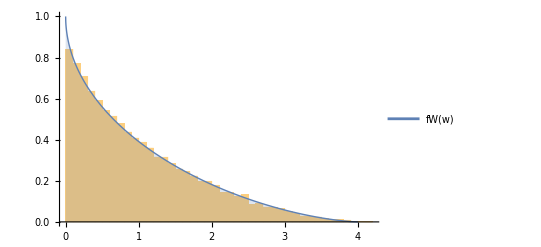

```mathematica
pk1=Histogram[distsq,40,"PDF"];
fW[w_]:=(2/Pi)*(ArcCos[Sqrt[w]/2]-(Sqrt[w]/2)*Sqrt[1-w/4])

pk2=Plot[fW[w],{w,0,4},PlotRange->All,PlotStyle->Thick,AxesLabel->{"w","f_W(w)"},PlotLabel->"PDF of Squared Interparticle Distance in a Unit Disc",Filling->Axis,PlotTheme->"Detailed"];

Show[pk1,pk2]
```

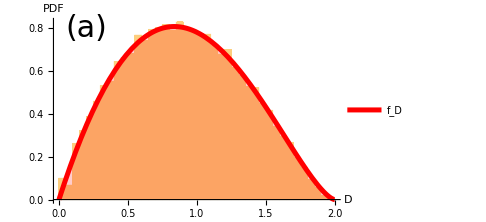

```mathematica
pk3=Histogram[distanceMatrix,40,"PDF"];
fD[d_]:=(4 d)/Pi (ArcCos[d/2]-(d/2) Sqrt[1-(d^2/4)])

pk4=Plot[fD[d],{d,0,2},PlotRange->All,PlotStyle->{Thickness[0.01],Red},AxesLabel->{"d","f_D(d)"},Filling->Axis,PlotTheme->"Detailed",AxesStyle->Thick,PlotLegends->{Style["f_D",Italic,25]}];

p901=Show[pk3,pk4,PlotRange->{{0,2},Automatic},AxesStyle->Thick,LabelStyle->20,AxesLabel->{Style["D",Bold,Italic,25],Style["PDF",Bold,25]},ImageSize->Medium,Epilog->{Text[Style["(a)",30],{0.2,0.8}]}]
```

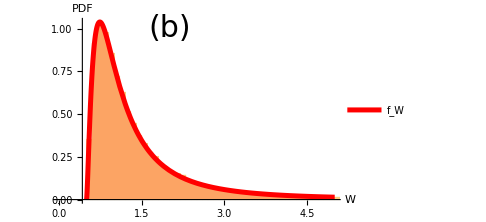

```mathematica
pk5=Histogram[invdist,150,"PDF"];
fU[u_]:=(4/(Pi u^3))*(ArcCos[1/(2 u)]-(1/(2 u)) Sqrt[1-1/(4 u^2)])

pk6=Plot[fU[u],{u,0.1,5},PlotRange->All,PlotStyle->{Thickness[0.01],Red},AxesLabel->{"u","f_U(u)"},Filling->Axis,PlotLegends->{Style["f_W",Italic,25]}];

p902=Show[pk5,pk6,AxesStyle->Thick,PlotRange->{{0,5},Automatic},LabelStyle->20,AxesLabel->{Style["W",Bold,Italic,25],Style["PDF",Bold,25]},ImageSize->Medium,Epilog->{Text[Style["(b)",30],{2,1}]}]
```

```mathematica
p903=Grid[{{p901,p902}}]
```

-Graphics- | -Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["figures/pdfs.png",p903];
```

```mathematica
R=1/(√1.5)
```

0.816497

```mathematica
fU[u_]:=(4/(Pi u^3 R^2))*(ArcCos[1/(2 u R)]-(1/(2 u R)) Sqrt[1-1/(4 u^2 R^2)])
meanU=NIntegrate[u*fU[u],{u,1/(2R),Infinity}]
1/meanU
```

2.07919

0.480956

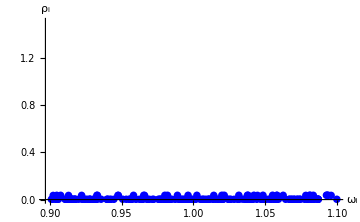

```mathematica
ListPlot[Transpose[{ω,AvFreq}],PlotStyle->{Blue,PointSize[0.015]},PlotRange->{All,{0,1.5}},AxesLabel->{"ω_i","ρ_i"},LabelStyle->20,AxesStyle->Thick,ImageSize->Medium]
```

```mathematica
Mean[AvFreq]
b=Commonest[Round[AvFreq,10^-1],1][[1]]
StandardDeviation[AvFreq]
Count[AvFreq,u_/;u<0.1]
Count[AvFreq,u_/;u<Mean[AvFreq]]
Count[AvFreq,u_/;u>b]
```

0.762786

0.7

0.0602884

0

375

500

```mathematica
Round[AvFreq,10^-1]//StandardDeviation
```

0.073157

```mathematica
Commonest[Round[AvFreq,10^-1],1][[1]]
```

0.7

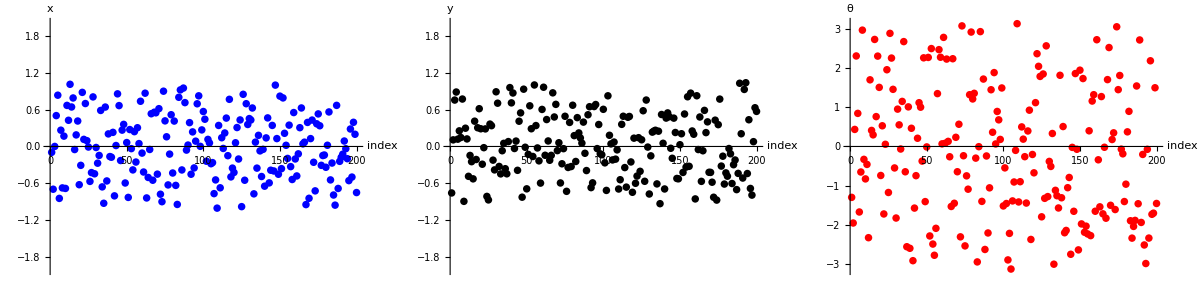

```mathematica
xnew=znew[[1,All]];
ynew=znew[[2,All]];
thetanew=znew[[3,All]]//mod;
p1=ListPlot[xnew,PlotStyle->{Blue,PointSize[0.015]},PlotRange->{All,{-2,2}},AxesLabel->{"index","x"},LabelStyle->15,AxesStyle->Thick,ImageSize->Medium];
p2=ListPlot[ynew,PlotStyle->{Black,PointSize[0.015]},PlotRange->{All,{-2,2}},AxesLabel->{"index","y"},LabelStyle->15,AxesStyle->Thick,ImageSize->Medium];
p3=ListPlot[thetanew,PlotStyle->{Red,PointSize[0.015]},PlotRange->{All,{-π,π}},AxesLabel->{"index","θ"},LabelStyle->15,AxesStyle->Thick,ImageSize->Medium];
p4=Grid[{{p1,p2,p3}}]
```

```mathematica
t
```

2000

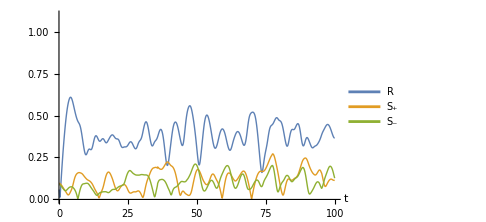

```mathematica
ListPlot[{Transpose[{ts,R//Abs}],Transpose[{ts,Sp//Abs}],Transpose[{ts,Sm//Abs}]},Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{0,1.1}},PlotLegends->{"R","S_+","S_-"},AxesLabel->{Style["t",Bold,Italic,25]},TicksStyle->Directive[Black, 20],AxesStyle->Thick,ImageSize->Medium]
```

## All states

### plot function

```mathematica
plotResults2[z_]:=Block[{colors,p1,p2,p3,Z,Wp,Wm,meanX,meanY,ϕ,θ},
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[z[[3,All]],2π]-1)/(2π)+380);
p1=Graphics[{PointSize[0.03],Point[{z[[1,All]],z[[2,All]]}ᵀ,VertexColors->colors]},
PlotRange->{{-1.2,1.2},{-1.2,1.2}},Axes->True,AspectRatio->1,ImageSize->Medium,AxesLabel->{Style["x",Bold,Italic,25],Style["y",Bold,Italic,25]},TicksStyle->Directive[Black, 20],AxesStyle->Thick,Epilog->{Text[Style["(c)",30],{-1,1}]}];

ϕ=ArcTan[z[[1,All]],z[[2,All]]];
θ=z[[3,All]];

p2=ListPlot[{ϕ//mod,θ//mod}ᵀ,PlotStyle->{PointSize[0.02],Blue},AxesLabel->{Style["ϕ",Bold,Italic,25],Style["θ",Bold,Italic,25]},TicksStyle->Directive[Black, 20],AxesStyle->Thick,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,Epilog->{Text[Style["(h)",30],{-2.75,2.75}]}];

{Z,Wp,Wm}=findOrderPars[z];
{meanX,meanY}={Mean[z[[1,All]]],Mean[z[[2,All]]]};

Return[Grid[{{p1},{p2}}]];

];
```

### sync

```mathematica
{dt,T,n}={0.1,200,200};
{A,B}={1,1};
{J1,k,γ}={0.5,0.6,0.1};
ω = RandomVariate[UniformDistribution[{1-γ,1+γ}],n];
z0=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
(*z0[[1,1]]=0.01;z0[[2,1]]=0.01;z0[[3,1]]=0;*)
znew=ConstantArray[0,{3,n}];

{t,NT}={0,Round[T/dt]};
results={};Dynamic[results]
{xs,ys,thetas,ts}={{},{},{},{}};
{R,Sp,Sm}={{},{},{}};
{vx,vtheta}={{},{}};
AvFreq = {};
While[t<NT,
znew=rk4[z0,rhslinearWinfreeNew,dt,J1,k,A,B,ω];
(*znew=periodizeMain[znew,1];*){x,y,θ}=znew;
{Z,Wp,Wm}=findOrderPars[znew];
z0=znew;t++;
velo=rhslinearWinfreeNew[znew,n,J1,k,A,B,ω];
PosVelo=Sqrt[velo[[1]]^2+velo[[2]]^2];
avPosVelo=Mean[PosVelo];avPhaseVelo=Mean[velo[[3]]];AppendTo[vx,avPosVelo];AppendTo[vtheta,avPhaseVelo];AppendTo[ts,t*dt];AppendTo[xs,x];AppendTo[ys,y];AppendTo[thetas,θ];AppendTo[R,Z];AppendTo[Sp,Wp];AppendTo[Sm,Wm];
If[t>Round[0.9*NT],AppendTo[AvFreq,θ/(t*dt)]];
(*results=plotResults[znew];*)
];
AvFreq=AvFreq//Mean;
```

```mathematica
zsync=znew;ωsync=ω;AvFreqsync=AvFreq;
```

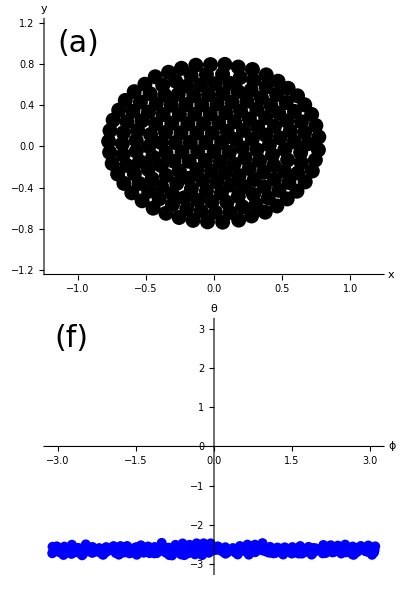
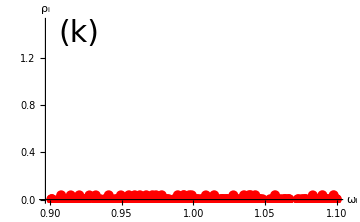

```mathematica
pq11=plotResults2[zsync];
pq12=ListPlot[Transpose[{ωsync,AvFreqsync}],PlotStyle->{Red,PointSize[0.02]},PlotRange->{All,{0,1.5}},AxesLabel->{Style["ω_i",Bold,Italic,25],Style["ρ_i",Bold,Italic,25]},TicksStyle->Directive[Black, 20],AxesStyle->Thick,ImageSize->Medium,Epilog->{Text[Style["(k)",30],{0.92,1.4}]}];
pq13=Grid[{{pq11},{pq12}}]
```

```mathematica
Rsync=R;Spsync=Sp;Smsync=Sm;
```

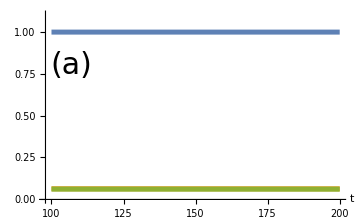

```mathematica
cutoff=0.5*Length[Rsync];
pq14=ListPlot[{Transpose[{ts[[cutoff;;-1]],Rsync[[cutoff;;-1]]//Abs}],Transpose[{ts[[cutoff;;-1]],Spsync[[cutoff;;-1]]//Abs}],Transpose[{ts[[cutoff;;-1]],Smsync[[cutoff;;-1]]//Abs}]},Joined->True,PlotStyle->Thickness[0.01],PlotRange->{Automatic,{0,1.1}},(*PlotLegends->{Style["R",25],Style["S_+",25],Style["S_-",25]},*)AxesLabel->{Style["t",Bold,Italic,25]},TicksStyle->Directive[Black, 20],AxesStyle->Thick,ImageSize->Medium,Epilog->{Text[Style["(a)",30],{107,0.8}]}]
```

```mathematica
vxsync = vx;vthetasync=vtheta;
```

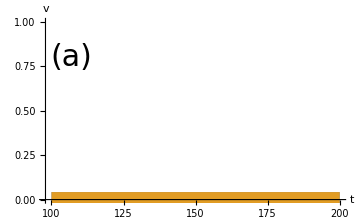

```mathematica
pq15=ListPlot[{Transpose[{ts[[cutoff;;-1]],vxsync[[cutoff;;-1]]}],Transpose[{ts[[cutoff;;-1]],vthetasync[[cutoff;;-1]]//Abs}]},Joined->True,PlotStyle->Thickness[0.03],PlotRange->{Automatic,{0,1}},(*PlotLegends->{Style["v_X",25],Style["v_θ",25]},*)AxesLabel->{Style["t",Bold,Italic,25],Style["v",Bold,Italic,25]},TicksStyle->Directive[Black, 20],AxesStyle->Thick,ImageSize->Medium,Epilog->{Text[Style["(a)",30],{107,0.8}]}]
```

### phase wave

```mathematica
{dt,T,n}={0.1,200,200};
{A,B}={1,1};
{J1,k,γ}={0.5,0.05,0.1};
ω = RandomVariate[UniformDistribution[{1-γ,1+γ}],n];
z0=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
(*z0[[1,1]]=0.01;z0[[2,1]]=0.01;z0[[3,1]]=0;*)
znew=ConstantArray[0,{3,n}];

{t,NT}={0,Round[T/dt]};
results={};Dynamic[results]
{xs,ys,thetas,ts}={{},{},{},{}};
{R,Sp,Sm}={{},{},{}};
{vx,vtheta}={{},{}};
AvFreq = {};
While[t<NT,
znew=rk4[z0,rhslinearWinfreeNew,dt,J1,k,A,B,ω];
(*znew=periodizeMain[znew,1];*){x,y,θ}=znew;
{Z,Wp,Wm}=findOrderPars[znew];
z0=znew;t++;
velo=rhslinearWinfreeNew[znew,n,J1,k,A,B,ω];
PosVelo=Sqrt[velo[[1]]^2+velo[[2]]^2];
avPosVelo=Mean[PosVelo];avPhaseVelo=Mean[velo[[3]]];AppendTo[vx,avPosVelo];AppendTo[vtheta,avPhaseVelo];AppendTo[ts,t*dt];AppendTo[xs,x];AppendTo[ys,y];AppendTo[thetas,θ];AppendTo[R,Z];AppendTo[Sp,Wp];AppendTo[Sm,Wm];
If[t>Round[0.9*NT],AppendTo[AvFreq,θ/(t*dt)]];
(*results=plotResults[znew];*)
];
AvFreq=AvFreq//Mean;
```

```mathematica
zpw=znew;ωpw=ω;AvFreqpw=AvFreq;
```

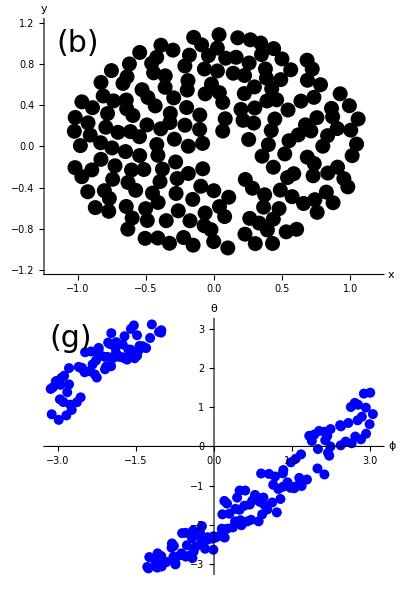
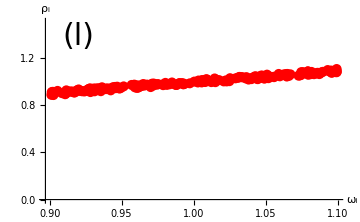

```mathematica
pq21=plotResults2[zpw];
pq22=ListPlot[Transpose[{ωpw,AvFreqpw}],PlotStyle->{Red,PointSize[0.02]},PlotRange->{All,{0,1.5}},AxesLabel->{Style["ω_i",Bold,Italic,25],Style["ρ_i",Bold,Italic,25]},TicksStyle->Directive[Black, 20],AxesStyle->Thick,ImageSize->Medium,Epilog->{Text[Style["(l)",30],{0.92,1.38}]}];
pq23=Grid[{{pq21},{pq22}}]
```

```mathematica
Rpw=R;Sppw=Sp;Smpw=Sm;
```

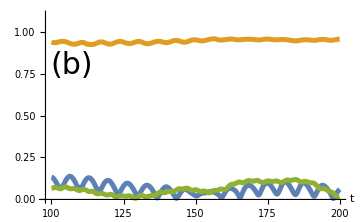

```mathematica
cutoff=0.5*Length[Rpw];
pq24=ListPlot[{Transpose[{ts[[cutoff;;-1]],Rpw[[cutoff;;-1]]//Abs}],Transpose[{ts[[cutoff;;-1]],Sppw[[cutoff;;-1]]//Abs}],Transpose[{ts[[cutoff;;-1]],Smpw[[cutoff;;-1]]//Abs}]},Joined->True,PlotStyle->Thickness[0.01],PlotRange->{Automatic,{0,1.1}},(*PlotLegends->{Style["R",25],Style["S_+",25],Style["S_-",25]},*)AxesLabel->{Style["t",Bold,Italic,25]},TicksStyle->Directive[Black, 20],AxesStyle->Thick,ImageSize->Medium,Epilog->{Text[Style["(b)",30],{107,0.8}]}]
```

```mathematica
vxpw = vx;vthetapw=vtheta;
```

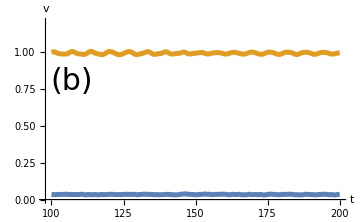

```mathematica
pq25=ListPlot[{Transpose[{ts[[cutoff;;-1]],vxpw[[cutoff;;-1]]}],Transpose[{ts[[cutoff;;-1]],vthetapw[[cutoff;;-1]]//Abs}]},Joined->True,PlotStyle->Thickness[0.01],PlotRange->{Automatic,{0,1.2}},(*PlotLegends->{Style["v_X",25],Style["v_θ",25]},*)AxesLabel->{Style["t",Bold,Italic,25],Style["v",Bold,Italic,25]},TicksStyle->Directive[Black, 20],AxesStyle->Thick,ImageSize->Medium,Epilog->{Text[Style["(b)",30],{107,0.8}]}]
```

### partial death

```mathematica
{dt,T,n}={0.1,200,200};
{A,B}={1,1};
{J1,k,γ}={0.5,0.4,0.6};
ω = RandomVariate[UniformDistribution[{1-γ,1+γ}],n];
z0=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
(*z0[[1,1]]=0.01;z0[[2,1]]=0.01;z0[[3,1]]=0;*)
znew=ConstantArray[0,{3,n}];

{t,NT}={0,Round[T/dt]};
results={};Dynamic[results]
{xs,ys,thetas,ts}={{},{},{},{}};
{R,Sp,Sm}={{},{},{}};
{vx,vtheta}={{},{}};
AvFreq = {};
While[t<NT,
znew=rk4[z0,rhslinearWinfreeNew,dt,J1,k,A,B,ω];
(*znew=periodizeMain[znew,1];*){x,y,θ}=znew;
{Z,Wp,Wm}=findOrderPars[znew];
z0=znew;t++;
velo=rhslinearWinfreeNew[znew,n,J1,k,A,B,ω];
PosVelo=Sqrt[velo[[1]]^2+velo[[2]]^2];
avPosVelo=Mean[PosVelo];avPhaseVelo=Mean[velo[[3]]];AppendTo[vx,avPosVelo];AppendTo[vtheta,avPhaseVelo];AppendTo[ts,t*dt];AppendTo[xs,x];AppendTo[ys,y];AppendTo[thetas,θ];AppendTo[R,Z];AppendTo[Sp,Wp];AppendTo[Sm,Wm];
If[t>Round[0.9*NT],AppendTo[AvFreq,θ/(t*dt)]];
(*results=plotResults[znew];*)
];
AvFreq=AvFreq//Mean;
```

```mathematica
zpd=znew;ωpd=ω;AvFreqpd=AvFreq;
```

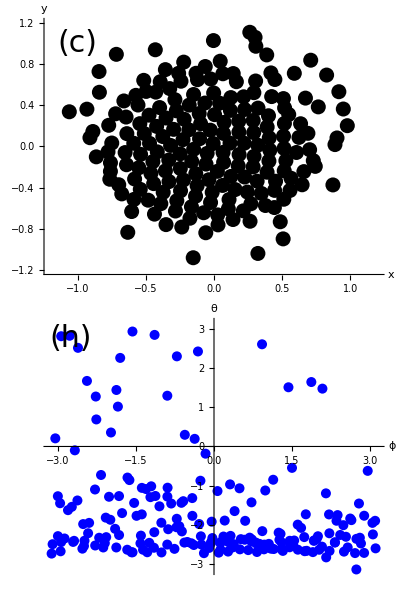
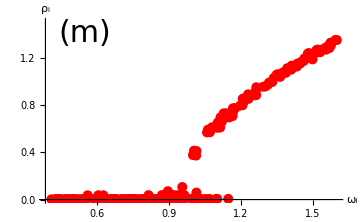

```mathematica
pq31=plotResults2[zpd];
pq32=ListPlot[Transpose[{ωpd,AvFreqpd}],PlotStyle->{Red,PointSize[0.02]},PlotRange->{All,{0,1.5}},AxesLabel->{Style["ω_i",Bold,Italic,25],Style["ρ_i",Bold,Italic,25]},TicksStyle->Directive[Black, 20],AxesStyle->Thick,ImageSize->Medium,Epilog->{Text[Style["(m)",30],{0.55,1.4}]}];
pq33=Grid[{{pq31},{pq32}}]
```

```mathematica
Rpd=R;Sppd=Sp;Smpd=Sm;
```

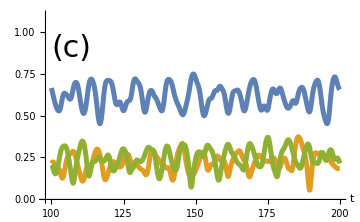

```mathematica
cutoff=0.5*Length[Rpd];
pq34=ListPlot[{Transpose[{ts[[cutoff;;-1]],Rpd[[cutoff;;-1]]//Abs}],Transpose[{ts[[cutoff;;-1]],Sppd[[cutoff;;-1]]//Abs}],Transpose[{ts[[cutoff;;-1]],Smpd[[cutoff;;-1]]//Abs}]},Joined->True,PlotStyle->Thickness[0.01],PlotRange->{Automatic,{0,1.1}},(*PlotLegends->{Style["R",25],Style["S_+",25],Style["S_-",25]},*)AxesLabel->{Style["t",Bold,Italic,25]},TicksStyle->Directive[Black, 20],AxesStyle->Thick,ImageSize->Medium,Epilog->{Text[Style["(c)",30],{107,0.9}]}]
```

```mathematica
vxpd = vx;vthetapd=vtheta;
```

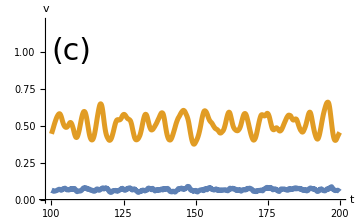

```mathematica
pq35=ListPlot[{Transpose[{ts[[cutoff;;-1]],vxpd[[cutoff;;-1]]}],Transpose[{ts[[cutoff;;-1]],vthetapd[[cutoff;;-1]]//Abs}]},Joined->True,PlotStyle->Thickness[0.01],PlotRange->{Automatic,{0,1.2}},(*PlotLegends->{Style["v_X",25],Style["v_θ",25]},*)AxesLabel->{Style["t",Bold,Italic,25],Style["v",Bold,Italic,25]},TicksStyle->Directive[Black, 20],AxesStyle->Thick,ImageSize->Medium,Epilog->{Text[Style["(c)",30],{107,1}]}]
```

### partial locking

```mathematica
{dt,T,n}={0.1,200,200};
{A,B}={1,1};
{J1,k,γ}={0.5,0.3,0.1};
ω = RandomVariate[UniformDistribution[{1-γ,1+γ}],n];
z0=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
(*z0[[1,1]]=0.01;z0[[2,1]]=0.01;z0[[3,1]]=0;*)
znew=ConstantArray[0,{3,n}];

{t,NT}={0,Round[T/dt]};
results={};Dynamic[results]
{xs,ys,thetas,ts}={{},{},{},{}};
{R,Sp,Sm}={{},{},{}};
{vx,vtheta}={{},{}};
AvFreq = {};
While[t<NT,
znew=rk4[z0,rhslinearWinfreeNew,dt,J1,k,A,B,ω];
(*znew=periodizeMain[znew,1];*){x,y,θ}=znew;
{Z,Wp,Wm}=findOrderPars[znew];
z0=znew;t++;
velo=rhslinearWinfreeNew[znew,n,J1,k,A,B,ω];
PosVelo=Sqrt[velo[[1]]^2+velo[[2]]^2];
avPosVelo=Mean[PosVelo];avPhaseVelo=Mean[velo[[3]]];AppendTo[vx,avPosVelo];AppendTo[vtheta,avPhaseVelo];AppendTo[ts,t*dt];AppendTo[xs,x];AppendTo[ys,y];AppendTo[thetas,θ];AppendTo[R,Z];AppendTo[Sp,Wp];AppendTo[Sm,Wm];
If[t>Round[0.9*NT],AppendTo[AvFreq,θ/(t*dt)]];
(*results=plotResults[znew];*)
];
AvFreq=AvFreq//Mean;
```

```mathematica
zpl=znew;ωpl=ω;AvFreqpl=AvFreq;
```

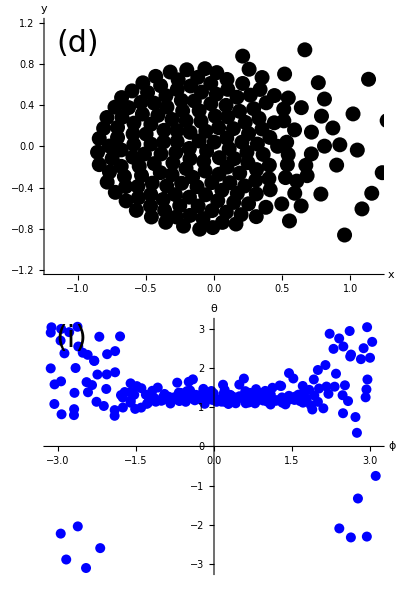
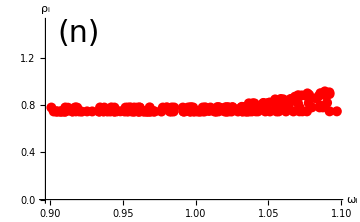

```mathematica
pq41=plotResults2[zpl];
pq42=ListPlot[Transpose[{ωpl,AvFreqpl}],PlotStyle->{Red,PointSize[0.02]},PlotRange->{All,{0,1.5}},AxesLabel->{Style["ω_i",Bold,Italic,25],Style["ρ_i",Bold,Italic,25]},TicksStyle->Directive[Black, 20],AxesStyle->Thick,ImageSize->Medium,Epilog->{Text[Style["(n)",30],{0.92,1.4}]}];
pq43=Grid[{{pq41},{pq42}}]
```

```mathematica
Rpl=R;Sppl=Sp;Smpl=Sm;
```

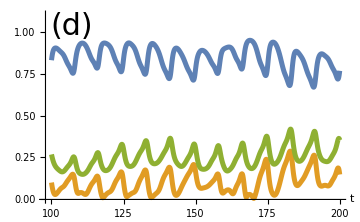

```mathematica
cutoff=0.5*Length[Rpl];
pq44=ListPlot[{Transpose[{ts[[cutoff;;-1]],Rpl[[cutoff;;-1]]//Abs}],Transpose[{ts[[cutoff;;-1]],Sppl[[cutoff;;-1]]//Abs}],Transpose[{ts[[cutoff;;-1]],Smpl[[cutoff;;-1]]//Abs}]},Joined->True,PlotStyle->Thickness[0.01],PlotRange->{Automatic,{0,1.1}},(*PlotLegends->{Style["R",25],Style["S_+",25],Style["S_-",25]},*)AxesLabel->{Style["t",Bold,Italic,25]},TicksStyle->Directive[Black, 20],AxesStyle->Thick,ImageSize->Medium,Epilog->{Text[Style["(d)",30],{107,1.03}]}]
```

```mathematica
vxpl = vx;vthetapl=vtheta;
```

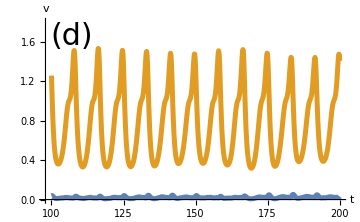

```mathematica
pq45=ListPlot[{Transpose[{ts[[cutoff;;-1]],vxpl[[cutoff;;-1]]}],Transpose[{ts[[cutoff;;-1]],vthetapl[[cutoff;;-1]]//Abs}]},Joined->True,PlotStyle->Thickness[0.01],PlotRange->{Automatic,{0,1.8}},(*PlotLegends->{Style["v_X",25],Style["v_θ",25]},*)AxesLabel->{Style["t",Bold,Italic,25],Style["v",Bold,Italic,25]},TicksStyle->Directive[Black, 20],AxesStyle->Thick,ImageSize->Medium,Epilog->{Text[Style["(d)",30],{107,1.65}]}]
```

### async

```mathematica
{dt,T,n}={0.1,200,200};
{A,B}={1,1};
{J1,k,γ}={0.5,0.2,0.6};
ω = RandomVariate[UniformDistribution[{1-γ,1+γ}],n];
z0=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
(*z0[[1,1]]=0.01;z0[[2,1]]=0.01;z0[[3,1]]=0;*)
znew=ConstantArray[0,{3,n}];

{t,NT}={0,Round[T/dt]};
results={};Dynamic[results]
{xs,ys,thetas,ts}={{},{},{},{}};
{R,Sp,Sm}={{},{},{}};
{vx,vtheta}={{},{}};
AvFreq = {};
While[t<NT,
znew=rk4[z0,rhslinearWinfreeNew,dt,J1,k,A,B,ω];
(*znew=periodizeMain[znew,1];*){x,y,θ}=znew;
{Z,Wp,Wm}=findOrderPars[znew];
z0=znew;t++;
velo=rhslinearWinfreeNew[znew,n,J1,k,A,B,ω];
PosVelo=Sqrt[velo[[1]]^2+velo[[2]]^2];
avPosVelo=Mean[PosVelo];avPhaseVelo=Mean[velo[[3]]];AppendTo[vx,avPosVelo];AppendTo[vtheta,avPhaseVelo];AppendTo[ts,t*dt];AppendTo[xs,x];AppendTo[ys,y];AppendTo[thetas,θ];AppendTo[R,Z];AppendTo[Sp,Wp];AppendTo[Sm,Wm];
If[t>Round[0.9*NT],AppendTo[AvFreq,θ/(t*dt)]];
(*results=plotResults[znew];*)
];
AvFreq=AvFreq//Mean;
```

```mathematica
zasync=znew;ωasync=ω;AvFreqasync=AvFreq;
```

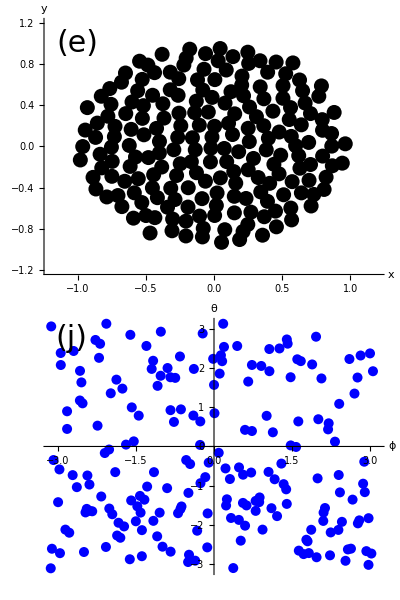
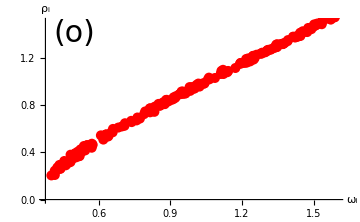

```mathematica
pq51=plotResults2[zasync];
pq52=ListPlot[Transpose[{ωasync,AvFreqasync}],PlotStyle->{Red,PointSize[0.02]},PlotRange->{All,{0,1.5}},AxesLabel->{Style["ω_i",Bold,Italic,25],Style["ρ_i",Bold,Italic,25]},TicksStyle->Directive[Black, 20],AxesStyle->Thick,ImageSize->Medium,Epilog->{Text[Style["(o)",30],{0.5,1.4}]}];
pq53=Grid[{{pq51},{pq52}}]
```

```mathematica
Ras=R;Spas=Sp;Smas=Sm;
```

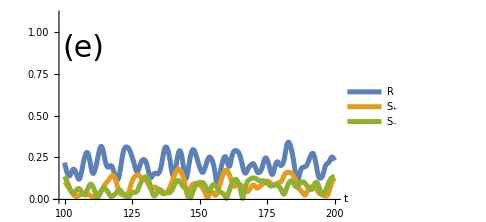

```mathematica
cutoff=0.5*Length[Ras];
pq54=ListPlot[{Transpose[{ts[[cutoff;;-1]],Ras[[cutoff;;-1]]//Abs}],Transpose[{ts[[cutoff;;-1]],Spas[[cutoff;;-1]]//Abs}],Transpose[{ts[[cutoff;;-1]],Smas[[cutoff;;-1]]//Abs}]},Joined->True,PlotStyle->Thickness[0.01],PlotRange->{Automatic,{0,1.1}},PlotLegends->{Style["R",Italic,25],Style["S_+",Italic,25],Style["S_-",Italic,25]},AxesLabel->{Style["t",Bold,Italic,25]},TicksStyle->Directive[Black, 20],AxesStyle->Thick,ImageSize->Medium,Epilog->{Text[Style["(e)",30],{107,0.9}]}]
```

```mathematica
vxas = vx;vthetaas=vtheta;
```

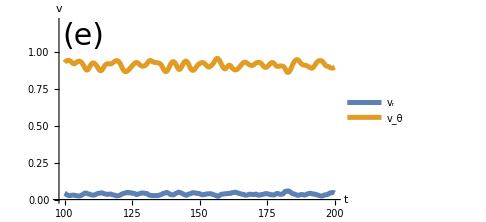

```mathematica
pq55=ListPlot[{Transpose[{ts[[cutoff;;-1]],vxas[[cutoff;;-1]]}],Transpose[{ts[[cutoff;;-1]],vthetaas[[cutoff;;-1]]//Abs}]},Joined->True,PlotStyle->Thickness[0.01],PlotRange->{Automatic,{0,1.2}},PlotLegends->{Style["v_r",Italic,25],Style["v_θ",Italic,25]},AxesLabel->{Style["t",Bold,Italic,25],Style["v",Bold,Italic,25]},TicksStyle->Directive[Black, 20],AxesStyle->Thick,ImageSize->Medium,Epilog->{Text[Style["(e)",30],{107,1.1}]}]
```

### plot together all states

```mathematica
pqnew=Grid[{{pq13,pq23,pq33,pq43,pq53}}]
```

-Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["figures/all-states2.png",pqnew];
```

### plot together order parameters

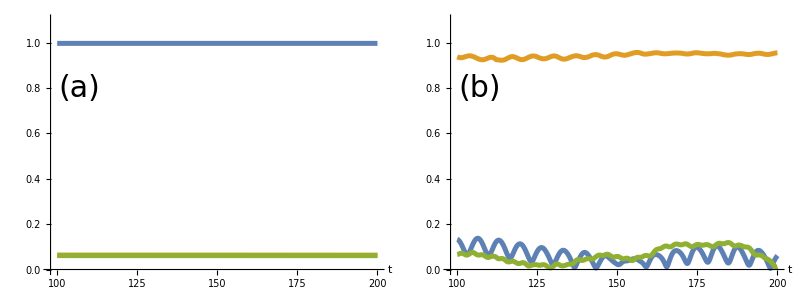
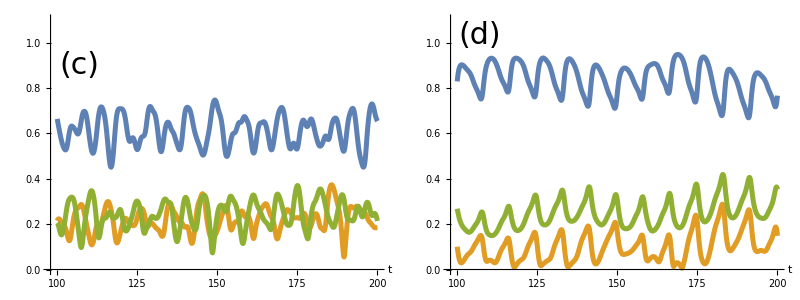
-Graphics-
-Graphics-
-Graphics-

```mathematica
pq100=Grid[{{pq14,pq24}}];
pq101=Grid[{{pq34,pq44}}];
pqnew1=Grid[{{pq100},{pq101},{pq54}}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["figures/order-parameters.png",pqnew1];
```

### plot together velocities

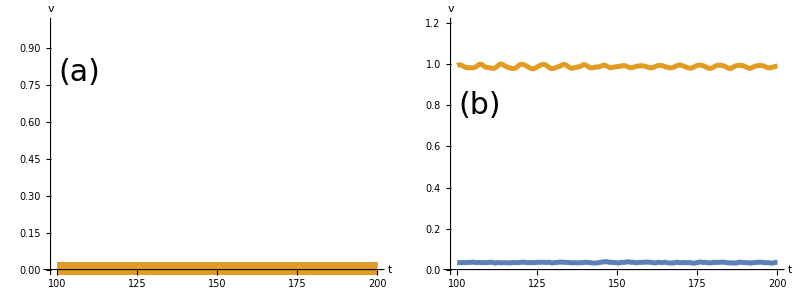
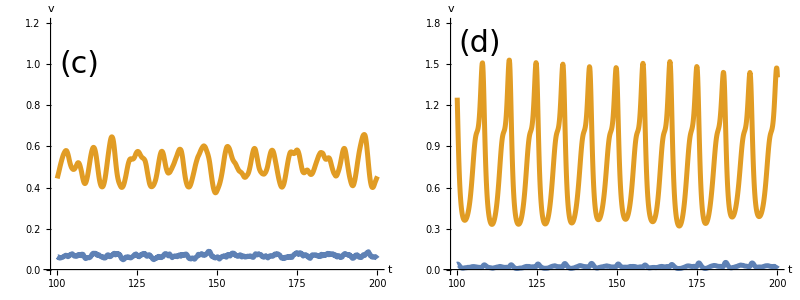
-Graphics-
-Graphics-
-Graphics-

```mathematica
pq200=Grid[{{pq15,pq25}}];
pq201=Grid[{{pq35,pq45}}];
pqnew2=Grid[{{pq200},{pq201},{pq55}}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["figures/velocities.png",pqnew2];
```

## K-γ space

### run

```mathematica
run[j1_,k1_,γ1_,T_,n_]:=Module[{J1,J2,K,γ,ω,A,B,dt,k,t,NT,z00,z0,znew,Z,Wp,Wm,Wp1,Wm1,xs,x,ys,y,θ,thetas,vmean,Sp,Sm,R,cutoff,AvFreq,Splus,Sminus,RR},

{dt}={0.1}; 
{J1,K,γ}={j1,k1,γ1};
J2=0;
{A,B}={1,1};
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
ω = RandomVariate[UniformDistribution[{1-γ,1+γ}],n];
z0=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
(*z0[[1,1]]=0.01;z0[[2,1]]=0.01;z0[[3,1]]=0;*)
znew=ConstantArray[0,{3,n}];

{xs,ys,thetas}={{},{},{}};
{R,Sp,Sm}={{},{},{}};
AvFreq = {};
While[t<NT,
znew=rk4[z0,rhslinearWinfreeNew,dt,J1,J2,K,A,B,ω];
(*znew=periodizeMain[znew,1];*){x,y,θ}=znew;
{Z,Wp,Wm}=findOrderPars[znew];
z0=znew;t++;AppendTo[xs,x];AppendTo[ys,y];AppendTo[thetas,θ];AppendTo[R,Z];AppendTo[Sp,Wp];AppendTo[Sm,Wm];
If[t>Round[0.9*NT],AppendTo[AvFreq,θ/(t*dt)]];
(*results=plotResults1[znew,zp0,L];*)
];
cutoff=Round[0.9Length[Sp]];
{Splus,Sminus,RR}={Abs[Sp[[cutoff;;-1]]]//Mean,Abs[Sm[[cutoff;;-1]]]//Mean,Abs[R[[cutoff;;-1]]]//Mean};
AvFreq=AvFreq//Mean;
Return[{Splus,Sminus,RR,Mean[AvFreq],Commonest[Round[AvFreq,10^-1],1][[1]],StandardDeviation[AvFreq]}]
]
```

### Make data

```mathematica
data=Flatten[ParallelTable[{γ,k,run[0.5,k,γ,100,200]}//Flatten,{γ,0,1,0.0125},{k,0,1,0.0125}],1];
```

```mathematica
6400*40/3600//N
```

71.1111

### Save data

```mathematica
SetDirectory[NotebookDirectory[]];
Export["data/K-γ-space-J=1.0-t=100-n=200-100-by-100.csv",data];
```

### Load data

```mathematica
SetDirectory[NotebookDirectory[]]
data1=Import["data/K-γ-space-J=0.5-t=100-n=200-100-by-100.csv"];
```

C:\Users\acer\Dropbox\winfree swarmalator 2d

### Color data

```mathematica
sps=data1[[All,3]];
sms=data1[[All,4]];
Rs=data1[[All,5]];
MeanFq=data1[[All,6]];
ModeFq=data1[[All,7]];
StdFq=data1[[All,8]];
temp=Table[
condSync=ModeFq[[i]]==0&&MeanFq[[i]]-ModeFq[[i]]<0.25;
condPartialDeath = ModeFq[[i]]==0&&MeanFq[[i]]-ModeFq[[i]]>0.25;
condAsync=ModeFq[[i]]≠0&&StdFq[[i]]>0.1;
condPW=ModeFq[[i]]≠0&&MeanFq[[i]]-ModeFq[[i]]<0.2&&Max[sps[[i]],sms[[i]]]>0.7;
condPartialLocked = ModeFq[[i]]≠0&&MeanFq[[i]]-ModeFq[[i]]<0.2&&StdFq[[i]]<0.1;
Which[condSync,"Sync",condPW,"Phase Wave",condPartialDeath,"Partial Death",condAsync,"Async",condPartialLocked,"Partial Locked"],
{i,1,Length[sps]}
];
Clear[colmap];
colmap[x1_]:=Which[x1=="Sync",Cyan,x1=="Phase Wave",Yellow,x1=="Partial Death", Red,x1=="Async",Magenta,x1=="Partial Locked",Blue];
SetAttributes[colmap,Listable];
alldata={data1[[All,1]],data1[[All,2]],temp//colmap}ᵀ;
```

### Plot data

```mathematica
p1=Graphics[Table[{alldata[[i,3]],Rectangle[{alldata[[i,1]],alldata[[i,2]]}]},{i,1,Length[alldata]}],
AspectRatio->1,PlotRange->{{0,1},{0,1}},Axes->True,LabelStyle->18,FrameLabel->{Style["γ",18,Italic],Style["K",18,Italic]},AxesStyle->Thick,PlotRangePadding->{{0.,-0.001},{0.,-0.00124}},Frame->True,Background->White,FrameStyle->Thick,
Epilog->{
Text[Style["Sync (death)",15],{0.5,0.75}],Text[Style["Partial death",15],{0.8,0.35}],Text[Style["Async",15],{0.5,0.1}],
Rotate[Text[Style["Partial \n locking",White,15],{0.07,0.27}],90 Degree],Rotate[Text[Style["Phase wave \n (locking)",15],{0.13,0.1}],45 Degree]
(*,Text[Style["(c)",25],{0.1,0.9}],Text[Style["J=1.0",Italic,20],{0.5,0.9}]*)},ImageSize->Medium];
p2=ContourPlot[k == 0.58(1-γ),{γ,0.32,1},{k,0,1},ContourStyle->{{Thick,Black},{Thick,Black}}];
p3=ContourPlot[k == 0.58*8γ/π,{γ,0,0.1},{k,0,0.45},ContourStyle->{{Thick,Black},{Thick,Black}}];
p4=ContourPlot[k == 0.58*8 γ/π*(1+(16 γ^2)/π^2+16*(π^2+80)/π^4*γ^4),{γ,0,1},{k,0,0.45},ContourStyle->{{Thick,Black},{Thick,Black}}];
p5=ContourPlot[1/(2.08*k) == 1/(4γ)*(2+π/2-(1-γ)/(1+γ)*(2+√(1-((1-γ)/(1+γ))^2))-ArcSin[(1-γ)/(1+γ)]),{γ,0,1},{k,0,1},ContourStyle->{{Thick,Black},{Thick,Black}}];
p6=ContourPlot[1/(2.08*k) == 1/(4γ)*(π/2+(1-γ)/(1+γ)*(√(1-((1-γ)/(1+γ))^2))-ArcSin[(1-γ)/(1+γ)]),{γ,0.32,1},{k,0,1},ContourStyle->{{Thick,Black},{Thick,Black}}];
p7=ContourPlot[2.08*k== G[1+γ]/F[1+γ],{γ,0,1},{k,0,1},ContourStyle->{{Thick,Black},{Thick,Black}}];
p8=ContourPlot[2.08k== AB,{γ,0,0.3},{k,0,1},ContourStyle->{{Thick,Black},{Thick,Black}}];
p11=Show[p1,p2,p5]
p893=p1;
```

-Graphics-

```mathematica
1/2.08
```

0.480769

```mathematica
p14=Grid[{{p891,p892,p893}}]
```

-Graphics-

```mathematica
Sqrt[1.5]/2
```

0.612372

### Save figure

```mathematica
SetDirectory[NotebookDirectory[]];
Export["figures/K-γ-space-J=0.1,0.5,1.0-t=100-n=200.png",p14];
```

### Calculations

```mathematica
G[σ_] := σ;
Gp = 1;
F[σ_] := 1+ σ/(4γ)*((1+γ)/σ*√(1-((1+γ)/σ)^2)-(1-γ)/σ*√(1-((1-γ)/σ)^2)+ArcSin[(1+γ)/σ]-ArcSin[(1-γ)/σ]);
```

```mathematica
DF1=D[F[σ],σ]//Simplify
```

-1/(4 γ σ)(√((-1-2 γ-γ^2+σ^2)/σ^2)+γ √((-1-2 γ-γ^2+σ^2)/σ^2)-√((-1+2 γ-γ^2+σ^2)/σ^2)+γ √((-1+2 γ-γ^2+σ^2)/σ^2)+σ ArcSin[(1-γ)/σ]-σ ArcSin[(1+γ)/σ])

```mathematica
G[1+γ]/F[1+γ];
```

```mathematica
Clear[k,DG,DF];
DG[σ_]:=1;
DF[σ_]:=-1/(4 γ σ)(√((-1-2 γ-γ^2+σ^2)/σ^2)+γ √((-1-2 γ-γ^2+σ^2)/σ^2)-√((-1+2 γ-γ^2+σ^2)/σ^2)+γ √((-1+2 γ-γ^2+σ^2)/σ^2)+σ ArcSin[(1-γ)/σ]-σ ArcSin[(1+γ)/σ]);
```

```mathematica
Solve[G[1+γ]/F[1+γ]==DG[1+γ]/DF[1+γ],γ]//N
```

{{γ→0.295598}}

```mathematica
Integrate[1/(2γ)√(1-(ω/σ)^2),{ω,1-γ,1+γ}]
```

$Aborted

```mathematica
D[z/2*√(1-z^2)+1/2 ArcSin[z],z]//Simplify
```

√(1-z^2)

```mathematica
A1=1+σ/(2γ)*(π/4-(1-γ)/(2(1+γ))*√(1-((1-γ)/(1+γ))^2)-1/2 ArcSin[(1-γ)/(1+γ)])//Simplify
```

1+(σ (4 (-1+γ) √(γ/(1+γ)^2)+π (1+γ)-2 (1+γ) ArcSin[(1-γ)/(1+γ)]))/(8 γ (1+γ))

```mathematica
A2=A1/k
```

(1+(σ (4 (-1+γ) √(γ/(1+γ)^2)+π (1+γ)-2 (1+γ) ArcSin[(1-γ)/(1+γ)]))/(8 γ (1+γ)))/k

```mathematica
σ*DF[σ]
F[σ]
```

-1/(4 γ)(√((-1-2 γ-γ^2+σ^2)/σ^2)+γ √((-1-2 γ-γ^2+σ^2)/σ^2)-√((-1+2 γ-γ^2+σ^2)/σ^2)+γ √((-1+2 γ-γ^2+σ^2)/σ^2)+σ ArcSin[(1-γ)/σ]-σ ArcSin[(1+γ)/σ])

1+(σ (-((1-γ) √(1-(1-γ)^2/σ^2))/σ+((1+γ) √(1-(1+γ)^2/σ^2))/σ-ArcSin[(1-γ)/σ]+ArcSin[(1+γ)/σ]))/(4 γ)

```mathematica
Solve[σ*DF[σ]==F[σ],σ]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

```mathematica
{{σ->-(2 √(-1-2 γ^2-γ^4))/(√(-3+2 γ^2+γ^4))},{σ->(2 √(-1-2 γ^2-γ^4))/(√(-3+2 γ^2+γ^4))}}
```

```mathematica
(2 √(-1-2 γ^2-γ^4))/(√(-3+2 γ^2+γ^4))/.γ->0.1
```

1.17017+0. ⅈ

```mathematica
AB=G[(2 √(-1-2 γ^2-γ^4))/(√(-3+2 γ^2+γ^4))]/F[(2 √(-1-2 γ^2-γ^4))/(√(-3+2 γ^2+γ^4))]//Simplify;
```

## Functions

```mathematica
rhslinearWinfree=Compile[{{z,_Real,2},{n,_Integer},{J1,_Real},{J2,_Real},{K,_Real},{A,_Real},{B,_Real},{ω,_Real,1}},
Module[{i,j,xji,yji,thetaji,inverseDistSq,distSq,dist,xtemp,ytemp,thetatemp,vel=ConstantArray[0.0,{3,n}]},
For[i=1,i≤n,i++,
For[j=1,j≤n,j++,
If[j!=i,
xji=z[[1,j]]-z[[1,i]];
yji=z[[2,j]]-z[[2,i]];
thetaji=z[[3,j]]-z[[3,i]];
distSq=xji^2+yji^2;
inverseDistSq=1/distSq;
dist=√distSq;
xtemp=xji((A + J1 Cos[thetaji])-(B-J2 Sin[thetaji]) inverseDistSq);
ytemp=yji((A + J1 Cos[thetaji])-(B-J2 Sin[thetaji]) inverseDistSq);
thetatemp=-K*Sin[z[[3,i]]]*(1+Cos[z[[3,j]]]) /dist; 
vel[[1,i]]+=xtemp/N[n];
vel[[2,i]]+=ytemp/N[n];
vel[[3,i]]+=ω[[i]]+thetatemp/N[n];];
];
];
vel
],
RuntimeAttributes->Listable,
Parallelization->True,
CompilationTarget->"C"
];

rhslinearWinfreeNew=Compile[{{z,_Real,2},{n,_Integer},{J1,_Real},{K,_Real},{A,_Real},{B,_Real},{ω,_Real,1}},
Module[{i,j,xji,yji,thetaji,inverseDistSq,distSq,dist,xtemp,ytemp,thetatemp,vel=ConstantArray[0.0,{3,n}]},
For[i=1,i≤n,i++,
For[j=1,j≤i-1,j++,
xji=z[[1,j]]-z[[1,i]];
yji=z[[2,j]]-z[[2,i]];
thetaji=z[[3,j]]-z[[3,i]];
distSq=xji^2+yji^2;
inverseDistSq=1/distSq;
dist=√distSq;
xtemp=xji((A + J1 Cos[thetaji])-B*inverseDistSq);
ytemp=yji((A + J1 Cos[thetaji])-B*inverseDistSq);
thetatemp=-K*Sin[z[[3,i]]]*(1+Cos[z[[3,j]]])/dist;
vel[[1,i]]+=xtemp/N[n];
vel[[2,i]]+=ytemp/N[n];
vel[[3,i]]+=thetatemp/N[n];
];
For[j=i+1,j≤n,j++,
xji=z[[1,j]]-z[[1,i]];
yji=z[[2,j]]-z[[2,i]];
thetaji=z[[3,j]]-z[[3,i]];
distSq=xji^2+yji^2;
inverseDistSq=1/distSq;
dist=√distSq;
xtemp=xji((A + J1 Cos[thetaji])-B*inverseDistSq);
ytemp=yji((A + J1 Cos[thetaji])-B*inverseDistSq);
thetatemp=-K*Sin[z[[3,i]]]*(1+Cos[z[[3,j]]])/dist; 
vel[[1,i]]+=xtemp/N[n];
vel[[2,i]]+=ytemp/N[n];
vel[[3,i]]+=thetatemp/N[n];
];
vel[[3,i]]+=ω[[i]];
];
vel
],
RuntimeAttributes->Listable,
Parallelization->True,
CompilationTarget->"C"
];




findNoise[d_,n_,dt_]:=Block[{noise,zeros},
If[d>0,
zeros=Table[0.0,{i,1,n}];
noise={zeros,zeros,RandomVariate[NormalDistribution[0,√dt],n]},
noise=Table[0.0,{i,1,3},{j,1,n}]
];
Return[noise];
]


rk4[z_,F_,dt_,J1_,K_,A_,B_,ω_]:=Block[{znew,n,i,j,k1,k2,k3,k4},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
k1=F[z,n,J1,K,A,B,ω];
k2=F[z+dt/2 k1,n,J1,K,A,B,ω];
k3=F[z+dt/2 k2,n,J1,K,A,B,ω];
k4=F[z+dt k3,n,J1,K,A,B,ω];
Return[z+dt/6(k1+2k2+2k3+k4)]
];

plotResults[z_]:=Block[{colors,p1,p2,p3,Z,Wp,Wm,meanX,meanY,ϕ,θ},
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[z[[3,All]],2π]-1)/(2π)+380);
p1=Graphics[{PointSize[0.03],Point[{z[[1,All]],z[[2,All]]}ᵀ,VertexColors->colors]},
PlotRange->{{-1.2,1.2},{-1.2,1.2}},Axes->True,AspectRatio->1,ImageSize->Medium,AxesLabel->{Style["x",Bold,Italic,25],Style["y",Bold,Italic,25]},TicksStyle->Directive[Black, 20],AxesStyle->Thick];

ϕ=ArcTan[z[[1,All]],z[[2,All]]];
θ=z[[3,All]];

p2=ListPlot[{ϕ//mod,θ//mod}ᵀ,PlotStyle->{PointSize[0.02],Blue},AxesLabel->{Style["ϕ",Bold,Italic,25],Style["θ",Bold,Italic,25]},TicksStyle->Directive[Black, 20],AxesStyle->Thick,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium];

{Z,Wp,Wm}=findOrderPars[z];
{meanX,meanY}={Mean[z[[1,All]]],Mean[z[[2,All]]]};

p3=Graphics[{PointSize[0.06],
Cyan,Point[{Z//Re,Z//Im}],Black,Text["Z",{Z//Re,Z//Im}],
Magenta,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Pink,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],
Blue,Point[{meanX,meanY}],Black,Text["⟨x⟩",{meanX,meanY}],
Circle[{0,0},1]
},AxesOrigin->{0,0},PlotRange->{{-1.1,1.1},{-1.1,1.1}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"Re(Z)","Im(Z)"},LabelStyle->15,ImageSize->Medium];

Return[Grid[{{p1,p2,p3}}]];

];


findOrderPars[z_]:=Block[{Z,Wp,Wm,R,i,numOsc,numPre,ϕ,θ},
{Z,Wp,Wm,R}={0,0,0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
{ϕ,θ}={ArcTan[z[[1,i]],z[[2,i]]],z[[3,i]]};
Z+=Exp[ⅈ θ];
Wp+=Exp[ⅈ(ϕ+θ)];
Wm+=Exp[ⅈ(ϕ-θ)];
];
Return[{Z/numOsc,Wp/numOsc,Wm/numOsc}]
];

findGamma[xs_,ys_]:=Block[{gamma,tolerance,phis,phi,s,temp,i,n},
n=Dimensions[xs][[2]];
gamma=0;
tolerance=0.05;
phis=ArcTan[xs,ys];
For[i=1,i≤n,i++,
phi=phis[[All,i]];
s=Sin[phi];
temp=(Max[s]-Min[s])/2;
If[temp>1-tolerance,gamma+=1];
];
Return[gamma/n]
];

findVelAutoCorr[xs_,ys_,n_,dt_]:=Block[{v,velAutoCorr},
velAutoCorr=Table[
v=Table[{Differences[xs[[All,i]]]/dt,Differences[ys[[All,i]]]/dt},{i,1,n}];
{τ dt,Mean[Table[Normalize[v[[i,All,1]]].Normalize[v[[i,All,τ]]],{i,1,n}]]},
{τ,1,Length[xs]-1}
];
Return[velAutoCorr]
];

findV[xs_,ys_,dt_,n_]:=Block[{v},
v=Table[{Differences[xs[[All,i]]]/dt,Differences[ys[[All,i]]]/dt},{i,1,n}];
Return[v]
];

findRijVijPairs[v_,xs_,ys_,t_,n_]:=Block[{dataRijVij,rij,vij,i,j},
dataRijVij={};
(*Iterate over all pairs*)
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
rij=((xs[[t,i]]-xs[[t,j]])^2+(ys[[t,i]]-ys[[t,j]])^2)^(1/2);
vij=Normalize[v[[i,All,t]]].Normalize[v[[j,All,t]]];
AppendTo[dataRijVij,{rij,vij}]
]
];
dataRijVij=Sort[dataRijVij];
Return[dataRijVij]
];

findCr[xs_,ys_,dt_,n_,t_]:=Block[{v,dataRijVij,rs,vs,groupedRs,groupedVs,k,binr,binv,i,j,Cr},
v=findV[xs,ys,dt,n];
dataRijVij=findRijVijPairs[v,xs,ys,t,n];

(*Parition values*)
{rs,vs}={dataRijVij[[All,1]],dataRijVij[[All,2]]};
groupedRs=BinLists[rs,{0,3,0.05}];
groupedVs={};
k=1;
For[i=1,i≤Length[groupedRs],i++,
binr=groupedRs[[i]];
binv={};
For[j=1,j≤Length[binr],j++,
AppendTo[binv,vs[[k]]];
k+=1;
];
AppendTo[groupedVs,binv]
];

(*Find averages values*)
Cr=Table[
{Mean[groupedRs[[i]]],Mean[groupedVs[[i]]]},
{i,1,Length[groupedRs]}
];
Return[Cr]
];

findGr[xs_,ys_,n_,t_]:=Block[{i,j,rijs,rij,rs,gs,dr,rmax},
(* Find g(r) := radial density *)

(*Find pairwise rij*)
rijs={};
(*Iterate over all pairs*)
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
rij=((xs[[t,i]]-xs[[t,j]])^2+(ys[[t,i]]-ys[[t,j]])^2)^(1/2);
AppendTo[rijs,rij]
]
];

(*Radial density*)
{dr,rmax}={0.1,2};
rs=Table[i,{i,0.05,rmax,dr}];
gs=BinLists[rijs,{0,rmax,dr}];
gs=Table[Length[gs[[i]]]/(n(n-1))//N,{i,1,Length[gs]}];

Return[{rs,gs}]
];

periodize[z_,L_]:=Block[{znext},
Which[
z>L,Return[-L],
z<-L,Return[L],
True,Return[z]
]
];
SetAttributes[periodize,Listable];

periodizeMain[znew_,L_]:=Block[{x,y,theta},
{x,y,theta}=znew;
{x,y}={periodize[x,L],periodize[y,L]};
Return[{x,y,theta}]
];


mod[θ_]:=Return[Mod[θ,2π]-π];

findVmean[xs_,ys_,thetas_,dt_]:=Module[{vx,vy,vtheta,tcutoff,vxMean,vyMean,vthetaMean,vMean,vxmean,n},{vx,vy,vtheta}={{},{},{}};
n=Dimensions[xs][[2]];
tcutoff=Round[0.5 Dimensions[xs][[1]]];
vxMean=Table[Mean[Differences[xs[[tcutoff;;-1,index]]]/dt],{index,1,n}]//Mean;
vyMean=Table[Mean[Differences[ys[[tcutoff;;-1,index]]]/dt],{index,1,n}]//Mean;
vthetaMean=Table[Mean[Differences[thetas[[tcutoff;;-1,index]]]/dt],{index,1,n}]//Mean;
vxmean=Sqrt[vxMean^2+vyMean^2];
vMean=Sqrt[vxMean^2+vyMean^2+vthetaMean^2];
Return[{vxmean,vMean}]]
```